{{S→InterpolatingFunction[…],M→InterpolatingFunction[…]}}

{{SS→InterpolatingFunction[…],MM→InterpolatingFunction[…]}}

{{SSS→InterpolatingFunction[…],MMM→InterpolatingFunction[…]}}

{{SSSS→InterpolatingFunction[…],MMMM→InterpolatingFunction[…]}}

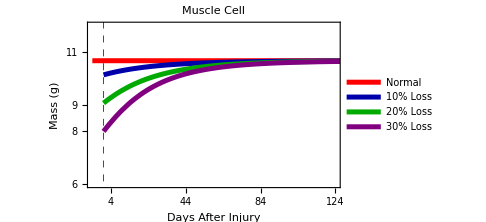

```mathematica
P0=0.479;P1=0.133;v0=0.087;v1=5.591;d=0.05;m=1000;
s1=NDSolve[{S'[x]==(2 *(P0+P1/(1+M[x]/m))-1)* (v0+v1/(1+M[x]/m))*S[x],M'[x]==2 *(1-P0-P1/(1+M[x]/m))* (v0+v1/(1+M[x]/m))* S[x]-d*M[x],S[0]==112.6,M[0]==2139.4},{S,M},{x,0,700}]
s2=NDSolve[{SS'[x]==(2 *(P0+P1/(1+MM[x]/m))-1)* (v0+v1/(1+MM[x]/m))*SS[x],MM'[x]==2 *(1-P0-P1/(1+MM[x]/m))* (v0+v1/(1+MM[x]/m))* SS[x]-d*MM[x],SS[376]==0.95*274.974,MM[376]==0.95*5333.33},{SS,MM},{x,376,1000}]
s3=NDSolve[{SSS'[x]==(2 *(P0+P1/(1+MMM[x]/m))-1)* (v0+v1/(1+MMM[x]/m))*SSS[x],MMM'[x]==2 *(1-P0-P1/(1+MMM[x]/m))* (v0+v1/(1+MMM[x]/m))* SSS[x]-d*MMM[x],SSS[376]==0.85*274.974,MMM[376]==0.85*5333.33},{SSS,MMM},{x,376,700}]
s4=NDSolve[{SSSS'[x]==(2 *(P0+P1/(1+MMMM[x]/m))-1)* (v0+v1/(1+MMMM[x]/m))*SSSS[x],MMMM'[x]==2 *(1-P0-P1/(1+MMMM[x]/m))* (v0+v1/(1+MMMM[x]/m))* SSSS[x]-d*MMMM[x],SSSS[376]==0.75*274.974,MMMM[376]==0.75*5333.33},{SSSS,MMMM},{x,376,700}]
p1=Plot[(0.002*M[x]/.s1),{x,370,700},PlotLegends->Placed[LineLegend[{"Normal"},LabelStyle->{FontSize->16,FontFamily->"Times New Roman"}],{0.78,0.6}],PlotRange->{{370,500},{6,12}},PlotStyle->{Red,Thickness[0.01]},GridLines->{{376},{}},GridLinesStyle->Directive[Black,Dashed](*,Ticks->{{{380,"4"},{385,""},{400,"24"},{420,"44"},{440,"64"},{460,"84"},{480,"104"},{500,"124"}},{6,7,8,9,10,11,12}}*)];
(*%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%*)
p2=Plot[(0.002*MM[x]/.s2),{x,376,700},PlotLegends->Placed[LineLegend[{"10% Loss"},LabelStyle->{FontSize->16,FontFamily->"Times New Roman"}],{0.8,0.5}],PlotRange->{{376,600},{0,20}},PlotStyle->{Darker[Blue],Thickness[0.01]}];

p3=Plot[(0.002*MMM[x]/.s3),{x,376,700},PlotLegends->Placed[LineLegend[{"20% Loss"},LabelStyle->{FontSize->16,FontFamily->"Times New Roman"}],{0.8,0.4}],PlotRange->{{376,600},{0,20}},PlotStyle->{Darker[Green],Thickness[0.01]}];

p4=Plot[(0.002*MMMM[x]/.s4),{x,376,700},PlotLegends->Placed[LineLegend[{"30% Loss"},LabelStyle->{FontSize->16,FontFamily->"Times New Roman"}],{0.8,0.3}],PlotRange->{{376,600},{0,20}},PlotStyle->{Purple,Thickness[0.01]}];

(*%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%*)
pl2s=Show[p1,p2,p3,p4,ImageSize->Medium,Frame->True,(*FrameLabel->{"Days after injury","Growth Ratio"},*)FrameLabel->{Style["Days After Injury",18(*,Bold*)],Style["Mass (g)",18(*,Bold*)]}(*FrameStyle->Directive[Black,12]*)(*ImageSize->400*),PlotLabel->"Muscle Cell",LabelStyle->Directive[(*Bold,*)Black,18,FontFamily->"Times New Roman"],FrameTicks->{{{380,"4"},{385,""},{390,""},{395,""},{400,"24"},{405,""},{410,""},{415,""},{420,"44"},{425,""},{430,""},{435,""},{440,"64"},{445,""},{450,""},{455,""},{460,"84"},{465,""},{470,""},{475,""},{480,"104"},{485,""},{490,""},{495,""},{500,"124"}},(*{6,7,8,9,10,11,12}*){{6,"6"},{6.25,""},{6.5,""},{6.75,""},{7,"7"},{7.25,""},{7.5,""},{7.75,""},{8,"8"},{8.25,""},{8.5,""},{8.75,""},{9,"9"},{8.25,""},{8.5,""},{8.75,""},{9,"9"},{9.25,""},{9.5,""},{9.75,""},{10,"10"},{10.25,""},{10.5,""},{10.75,""},{11,"11"},{11.25,""},{11.5,""},{11.75,""},{12,"12"}},Automatic,Automatic},FrameTicksStyle->Directive[Black,14]]
```

```mathematica
For[x=376,x≤700,x+=1,
x1=376;
(*If[((MMM[x]/.s3)[[1]]-(M[376]/.s1)[[1]])<0.01,*)
Print[x-x1,"    ",Abs[(0.002*M[376]/.s1)[[1]]-(0.002*MM[x]/.s2)[[1]]],"    ",Abs[(0.002*M[376]/.s1)[[1]]-(0.002*MMM[x]/.s3)[[1]]],"    ",Abs[(0.002*M[376]/.s1)[[1]]-(0.002*MMMM[x]/.s4)[[1]]]]]
```

0    0.533343    1.60001    2.66667

1    0.514394    1.54431    2.5761

2    0.496134    1.4903    2.48751

3    0.478538    1.43795    2.40098

4    0.461582    1.38724    2.31659

5    0.445243    1.33814    2.23439

6    0.4295    1.29064    2.15442

7    0.414331    1.24468    2.07669

8    0.399714    1.20025    2.00123

9    0.385631    1.1573    1.92803

10    0.37206    1.1158    1.85708

11    0.358985    1.07572    1.78837

12    0.346386    1.03701    1.72188

13    0.334245    0.999652    1.65758

14    0.322547    0.963593    1.59542

15    0.311274    0.928801    1.53538

16    0.300411    0.895238    1.47742

17    0.289943    0.862867    1.42148

18    0.279855    0.831652    1.36752

19    0.270133    0.801556    1.3155

20    0.260763    0.772544    1.26535

21    0.251732    0.744581    1.21704

22    0.243028    0.717632    1.17051

23    0.234638    0.691664    1.1257

24    0.22655    0.666643    1.08256

25    0.218754    0.642537    1.04105

26    0.211239    0.619315    1.00111

27    0.203993    0.596945    0.96268

28    0.197007    0.575399    0.925722

29    0.190272    0.554647    0.890182

30    0.183778    0.53466    0.85601

31    0.177515    0.515412    0.823159

32    0.171476    0.496875    0.791581

33    0.165652    0.479024    0.761231

34    0.160035    0.461833    0.732063

35    0.154617    0.44528    0.704035

36    0.149391    0.429339    0.677103

37    0.14435    0.413989    0.651227

38    0.139487    0.399208    0.626367

39    0.134796    0.384974    0.602484

40    0.130269    0.371267    0.57954

41    0.125902    0.358068    0.557499

42    0.121688    0.345357    0.536327

43    0.117621    0.333116    0.515989

44    0.113696    0.321327    0.496453

45    0.109908    0.309973    0.477687

46    0.106253    0.299039    0.45966

47    0.102724    0.288507    0.442344

48    0.0993173    0.278363    0.42571

49    0.0960289    0.268593    0.409731

50    0.092854    0.259181    0.39438

51    0.0897886    0.250115    0.379633

52    0.0868289    0.241381    0.365466

53    0.0839711    0.232966    0.351854

54    0.0812114    0.224859    0.338776

55    0.078546    0.217048    0.326211

56    0.0759717    0.209522    0.314137

57    0.0734854    0.202269    0.302534

58    0.0710838    0.19528    0.291384

59    0.068764    0.188544    0.280668

60    0.0665227    0.182053    0.270369

61    0.0643575    0.175796    0.26047

62    0.0622655    0.169764    0.250955

63    0.0602443    0.16395    0.241807

64    0.0582912    0.158345    0.233014

65    0.0564037    0.152942    0.224559

66    0.0545797    0.147732    0.216429

67    0.0528169    0.142708    0.208612

68    0.0511132    0.137863    0.201094

69    0.0494664    0.133192    0.193863

70    0.0478745    0.128686    0.186909

71    0.0463357    0.12434    0.18022

72    0.0448481    0.120149    0.173784

73    0.0434099    0.116105    0.167593

74    0.0420194    0.112204    0.161636

75    0.0406749    0.108441    0.155904

76    0.0393749    0.10481    0.150388

77    0.0381178    0.101306    0.145079

78    0.0369021    0.0979253    0.139969

79    0.0357265    0.0946625    0.13505

80    0.0345894    0.0915135    0.130315

81    0.0334896    0.0884742    0.125756

82    0.0324259    0.0855406    0.121366

83    0.031397    0.0827086    0.117139

84    0.0304017    0.0799746    0.113069

85    0.0294388    0.0773352    0.109148

86    0.0285073    0.0747867    0.105371

87    0.0276061    0.0723259    0.101733

88    0.0267343    0.0699497    0.0982284

89    0.0258907    0.0676549    0.0948514

90    0.0250745    0.0654386    0.0915974

91    0.0242846    0.0632981    0.0884618

92    0.0235202    0.0612305    0.0854398

93    0.0227806    0.0592332    0.0825269

94    0.0220648    0.0573037    0.079719

95    0.0213721    0.0554398    0.0770123

96    0.0207016    0.0536389    0.0744027

97    0.0200526    0.0518989    0.0718864

98    0.0194244    0.0502174    0.06946

99    0.0188165    0.0485925    0.0671201

100    0.018228    0.0470222    0.0648634

101    0.0176583    0.0455047    0.0626866

102    0.0171068    0.044038    0.0605868

103    0.0165728    0.0426202    0.0585611

104    0.0160559    0.0412497    0.0566068

105    0.0155554    0.0399249    0.054721

106    0.0150709    0.0386442    0.0529013

107    0.0146018    0.037406    0.0511453

108    0.0141476    0.0362088    0.0494505

109    0.0137077    0.0350512    0.0478147

110    0.0132818    0.0339319    0.0462355

111    0.0128693    0.0328495    0.0447111

112    0.01247    0.0318028    0.0432394

113    0.0120832    0.0307905    0.0418186

114    0.0117087    0.0298113    0.0404467

115    0.0113459    0.0288643    0.0391217

116    0.0109946    0.0279484    0.0378421

117    0.0106543    0.0270624    0.0366063

118    0.0103248    0.0262052    0.0354127

119    0.0100056    0.025376    0.0342598

120    0.0096964    0.0245738    0.0331461

121    0.00939691    0.0237977    0.03207

122    0.00910681    0.0230468    0.0310303

123    0.00882581    0.0223202    0.0300258

124    0.00855362    0.0216171    0.0290551

125    0.00828995    0.0209367    0.0281172

126    0.00803451    0.0202784    0.0272106

127    0.00778704    0.0196412    0.0263344

128    0.00754729    0.0190246    0.0254875

129    0.00731503    0.0184278    0.024669

130    0.00709002    0.0178501    0.0238777

131    0.00687203    0.0172911    0.0231127

132    0.00666081    0.0167499    0.0223731

133    0.00645615    0.0162261    0.021658

134    0.00625786    0.015719    0.0209666

135    0.00606574    0.0152281    0.020298

136    0.00587959    0.0147529    0.0196515

137    0.00569922    0.0142928    0.0190263

138    0.00552445    0.0138474    0.0184215

139    0.00535508    0.0134162    0.0178366

140    0.00519096    0.0129986    0.0172709

141    0.00503192    0.0125942    0.0167237

142    0.00487782    0.0122028    0.0161944

143    0.00472849    0.0118237    0.0156824

144    0.00458378    0.0114566    0.0151869

145    0.00444352    0.0111012    0.0147076

146    0.00430759    0.0107569    0.0142439

147    0.00417587    0.0104235    0.0137952

148    0.00404821    0.0101006    0.013361

149    0.00392451    0.00978792    0.0129409

150    0.00380462    0.00948508    0.0125343

151    0.00368842    0.00919175    0.0121408

152    0.00357579    0.00890762    0.01176

153    0.00346663    0.00863242    0.0113914

154    0.00336083    0.00836586    0.0110347

155    0.0032583    0.00810767    0.0106894

156    0.00315892    0.00785757    0.0103552

157    0.0030626    0.00761528    0.0100317

158    0.00296924    0.00738056    0.00971849

159    0.00287873    0.00715318    0.00941531

160    0.00279101    0.00693291    0.00912178

161    0.00270598    0.00671953    0.0088376

162    0.00262357    0.0065128    0.00856246

163    0.00254368    0.0063125    0.00829607

164    0.00246625    0.00611844    0.00803815

165    0.0023912    0.00593041    0.00778841

166    0.00231843    0.00574825    0.00754656

167    0.00224789    0.00557176    0.00731237

168    0.00217952    0.00540075    0.00708559

169    0.00211324    0.00523503    0.00686598

170    0.002049    0.00507446    0.0066533

171    0.00198672    0.00491886    0.00644733

172    0.00192635    0.0047681    0.00624783

173    0.00186781    0.00462202    0.00605461

174    0.00181107    0.00448046    0.00586748

175    0.00175606    0.00434328    0.00568623

176    0.00170274    0.00421034    0.00551067

177    0.00165105    0.0040815    0.0053406

178    0.00160094    0.00395664    0.00517587

179    0.00155236    0.00383565    0.0050163

180    0.00150526    0.0037184    0.00486172

181    0.00145959    0.00360477    0.00471199

182    0.00141532    0.00349464    0.00456692

183    0.0013724    0.0033879    0.00442638

184    0.0013308    0.00328444    0.00429023

185    0.00129046    0.00318418    0.00415832

186    0.00125136    0.003087    0.00403053

187    0.00121344    0.00299283    0.00390672

188    0.00117668    0.00290155    0.00378675

189    0.00114103    0.00281307    0.00367051

190    0.00110648    0.00272731    0.00355788

191    0.00107298    0.00264418    0.00344875

192    0.00104051    0.0025636    0.00334302

193    0.00100902    0.00248551    0.00324058

194    0.00097849    0.00240982    0.0031413

195    0.000948886    0.00233645    0.0030451

196    0.000920182    0.00226532    0.00295187

197    0.000892352    0.00219637    0.00286152

198    0.000865371    0.00212954    0.00277398

199    0.000839212    0.00206476    0.00268915

200    0.000813852    0.00200196    0.00260694

201    0.000789263    0.00194109    0.00252727

202    0.00076542    0.00188209    0.00245006

203    0.0007423    0.00182488    0.00237522

204    0.000719882    0.00176943    0.00230269

205    0.000698146    0.00171567    0.0022324

206    0.000677071    0.00166356    0.00216428

207    0.000656639    0.00161304    0.00209826

208    0.00063683    0.00156407    0.00203427

209    0.000617622    0.0015166    0.00197225

210    0.000598997    0.00147057    0.00191213

211    0.000580936    0.00142594    0.00185386

212    0.000563422    0.00138268    0.00179738

213    0.000546441    0.00134074    0.00174264

214    0.000529976    0.00130009    0.00168959

215    0.000514013    0.00126068    0.00163817

216    0.000498536    0.00122247    0.00158832

217    0.000483528    0.00118543    0.00153999

218    0.000468975    0.00114951    0.00149315

219    0.000454863    0.00111468    0.00144774

220    0.000441178    0.00108091    0.00140373

221    0.000427908    0.00104818    0.00136108

222    0.000415042    0.00101645    0.00131973

223    0.000402568    0.000985684    0.00127964

224    0.000390473    0.000955858    0.00124077

225    0.000378745    0.000926939    0.0012031

226    0.000367372    0.000898897    0.00116658

227    0.000356342    0.000871707    0.00113118

228    0.000345647    0.000845346    0.00109686

229    0.000335276    0.000819788    0.00106359

230    0.000325221    0.00079501    0.00103134

231    0.000315471    0.000770988    0.00100007

232    0.000306018    0.000747697    0.000969755

233    0.000296851    0.000725114    0.000940366

234    0.000287961    0.000703215    0.000911877

235    0.00027934    0.000681981    0.000884258

236    0.000270979    0.000661392    0.000857484

237    0.000262873    0.000641431    0.000831526

238    0.000255012    0.000622078    0.000806357

239    0.000247391    0.000603315    0.000781955

240    0.000240002    0.000585122    0.000758298

241    0.000232837    0.000567481    0.000735363

242    0.00022589    0.000550375    0.000713129

243    0.000219152    0.000533786    0.000691573

244    0.000212618    0.000517702    0.000670674

245    0.00020628    0.000502107    0.000650409

246    0.000200134    0.000486988    0.00063076

247    0.000194174    0.000472328    0.000611711

248    0.000188395    0.000458114    0.000593242

249    0.000182792    0.000444331    0.000575336

250    0.000177359    0.000430964    0.000557976

251    0.000172091    0.000418003    0.000541145

252    0.000166983    0.000405435    0.000524824

253    0.00016203    0.000393249    0.000508998

254    0.000157225    0.000381434    0.000493653

255    0.000152566    0.000369978    0.000478776

256    0.000148047    0.000358871    0.000464352

257    0.000143665    0.000348099    0.000450369

258    0.000139416    0.000337653    0.000436812

259    0.000135296    0.000327524    0.000423668

260    0.000131302    0.000317701    0.000410923

261    0.000127429    0.000308177    0.000398564

262    0.000123673    0.000298943    0.000386578

263    0.000120031    0.000289989    0.000374955

264    0.000116499    0.000281309    0.000363685

265    0.000113073    0.000272891    0.000352758

266    0.00010975    0.000264729    0.000342164

267    0.000106528    0.000256813    0.000331893

268    0.000103404    0.000249135    0.000321935

269    0.000100375    0.000241689    0.00031228

270    0.0000974384    0.000234469    0.000302917

271    0.0000945905    0.000227468    0.000293837

272    0.000091829    0.000220681    0.000285031

273    0.0000891508    0.000214099    0.000276492

274    0.0000865531    0.000207718    0.000268212

275    0.0000840336    0.00020153    0.000260184

276    0.0000815902    0.00019553    0.000252401

277    0.0000792209    0.00018971    0.000244855

278    0.0000769234    0.000184066    0.000237539

279    0.0000746958    0.000178592    0.000230444

280    0.0000725359    0.000173285    0.000223564

281    0.0000704414    0.000168139    0.000216891

282    0.0000684105    0.000163149    0.00021042

283    0.0000664408    0.000158311    0.000204146

284    0.0000645304    0.00015362    0.000198062

285    0.0000626775    0.000149071    0.000192163

286    0.0000608806    0.000144659    0.000186444

287    0.0000591382    0.00014038    0.000180899

288    0.0000574486    0.000136231    0.000175522

289    0.0000558104    0.000132207    0.000170307

290    0.0000542219    0.000128305    0.00016525

291    0.0000526817    0.000124522    0.000160346

292    0.0000511881    0.000120853    0.00015559

293    0.0000497395    0.000117296    0.000150978

294    0.0000483345    0.000113847    0.000146506

295    0.0000469717    0.000110503    0.00014217

296    0.00004565    0.000107259    0.000137966

297    0.0000443683    0.000104113    0.00013389

298    0.0000431255    0.000101061    0.000129937

299    0.0000419204    0.0000981023    0.000126104

300    0.0000407521    0.000095233    0.000122386

301    0.0000396194    0.000092451    0.00011878

302    0.0000385211    0.0000897534    0.000115284

303    0.0000374562    0.0000871377    0.000111893

304    0.0000364236    0.0000846014    0.000108606

305    0.0000354222    0.0000821418    0.000105419

306    0.0000344509    0.0000797562    0.000102328

307    0.0000335086    0.0000774425    0.0000993316

308    0.0000325942    0.0000751986    0.0000964255

309    0.0000317069    0.0000730228    0.0000936071

310    0.0000308461    0.0000709129    0.0000908736

311    0.0000300112    0.0000688671    0.0000882228

312    0.0000292015    0.0000668835    0.0000856524

313    0.0000284163    0.00006496    0.00008316

314    0.0000276549    0.0000630947    0.0000807432

315    0.0000269168    0.0000612857    0.0000783997

316    0.0000262012    0.0000595312    0.0000761271

317    0.0000255075    0.0000578297    0.0000739231

318    0.000024835    0.0000561797    0.0000717856

319    0.0000241831    0.0000545798    0.0000697128

320    0.0000235512    0.0000530285    0.0000677027

321    0.0000229384    0.0000515242    0.0000657537

322    0.000022344    0.0000500656    0.0000638637

323    0.0000217673    0.000048651    0.0000620311

324    0.0000212079    0.0000472791    0.000060254